Configuration and functions

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ManualLabel=Function[{aud,durr},
Print[AudioPlot[aud]];
(*Split th audio*)
fragments=AudioPartition[aud,durr];
(*Manual label*)
labels=Table[
AudioPlay[f];
label=InputString[{f,AudioPlot[f],"Label:"}];
StringSplit[label,","],
{f,fragments}
];
(*Join fragments with labels*)
Thread[Rule[fragments,labels]]
];
```

Load files

```mathematica
files=FileNames["aud*.mp3","./Resources"];
audios=Import/@files
```

{,,,,}

Manual label for all partitions

```mathematica
labelPartitions=Table[
ManualLabel[audio,Quantity[100,"Milliseconds"]]
,{audio,audios}];
```

```mathematica
Export["./Resources/labelPartition.json",labelPartitions[[All,All,2]],"JSON"]
```

./Resources/labelPartition.json

Import and zip partitions

```mathematica
partitions=Table[
AudioPartition[audio,Quantity[100,"Milliseconds"]]
,{audio,audios}];
```

```mathematica
labels=Import["./Resources/labelPartition.json","JSON"]
```

{{{S},{S},{S},{S},{S,V},{S,U},{S},{U},{V},{S,V},{V},{U,S},{V},{V},{U},{V},{S},{S},{S}},{{S},{S},{S},{S,U},{V},{U},{U,V},{V,U},{V},{U},{V,U},{U},{V},{V},{V,S},{U},{U},{V},{V},{U},{S},{S},{S},{S}},{{S},{S},{S,U},{V},{U},{U,V},{V},{V},{U},{V},{U},{U},{U},{V},{V},{V},{U},{U},{V},{U},{U,S},{S}},{{S},{S,U},{V},{U,V},{V},{V},{U},{S,V},{V},{V},{V},{V},{S,U},{V,U},{U},{V},{S},{S},{S}},{{S},{S},{S},{S},{S,V},{V},{V},{V},{V,U},{V,U},{V},{V},{V,U},{S,U},{U,S},{S,U},{V,U},{V},{S},{V},{V},{V},{U,V},{V,U},{V},{S,U},{V},{V},{S,U},{S},{S},{S}}}

```mathematica
labelPartitions=MapThread[Thread[#1->#2]&,{partitions,labels}];
```

```mathematica
flatLabelPartitions=Flatten[labelPartitions];
s=Select[flatLabelPartitions,MemberQ[#[[2]],"S"]&][[All,1]];
u=Select[flatLabelPartitions,MemberQ[#[[2]],"U"]&][[All,1]];
v=Select[flatLabelPartitions,MemberQ[#[[2]],"V"]&][[All,1]];
```

```mathematica
sTrain=s[[1;;IntegerPart[0.8 Length[s]]]];
sTest=s[[IntegerPart[0.8 Length[s]];;Length[s]]];

uTrain=u[[1;;IntegerPart[0.8 Length[u]]]];
uTest=u[[IntegerPart[0.8 Length[u]];;Length[u]]];

vTrain=v[[1;;IntegerPart[0.8 Length[v]]]];
vTest=v[[IntegerPart[0.8 Length[v]];;Length[v]]];
```

```mathematica
vTrain[[1]];
Length[AudioData[vTrain[[1]]][[1]]]
AudioSampleRate[vTrain[[1]]]
```

4800

48000 Hz

```mathematica
enc=NetEncoder["AudioMFCC"];
```

```mathematica
sLabeled=Thread[enc[sTrain]->"S"];
uLabeled=Thread[enc[uTrain]->"U"];
vLabeled=Thread[enc[vTrain]->"V"];
```

```mathematica
Print[Length[sLabeled],Dimensions[sLabeled[[1,1]]]]
Print[Length[uLabeled],Dimensions[uLabeled[[1,1]]]]
Print[Length[vLabeled],Dimensions[vLabeled[[1,1]]]]
```

37{12,13}

33{12,13}

44{12,13}

```mathematica
trainingData=Join[sLabeled,uLabeled,vLabeled]
```

```mathematica
sTestLabeled=Thread[enc[sTest]->"S"];
uTestLabeled=Thread[enc[uTest]->"U"];
vTestLabeled=Thread[enc[vTest]->"V"];

testData=Join[sTestLabeled,uTestLabeled,vTestLabeled];
```

```mathematica
bayesianInference=Classify[trainingData,Method->"NaiveBayes"];
decisionTree=Classify[trainingData,Method->"DecisionTree"];
neuronalNetwork=Classify[Join[trainingData,testData],Method->"NeuralNetwork"];
```

```mathematica
cmBI=ClassifierMeasurements[bayesianInference,testData];
cmDT=ClassifierMeasurements[decisionTree,testData];
cmNN=ClassifierMeasurements[neuronalNetwork,testData];
```

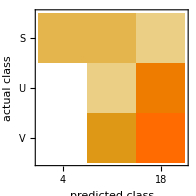

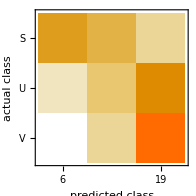

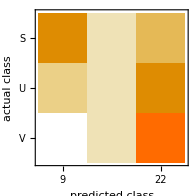

```mathematica
cmBI["ConfusionMatrixPlot"]
cmDT["ConfusionMatrixPlot"]
cmNN["ConfusionMatrixPlot"]
```

```mathematica
cmBI[{"Accuracy","Precision","Recall","F1Score"}]
cmDT[{"Accuracy","Precision","Recall","F1Score"}]
cmNN[{"Accuracy","Precision","Recall","F1Score"}]
```

{0.441176,<|S→1.,U→0.25,V→0.444444|>,<|S→0.363636,U→0.3,V→0.615385|>,<|S→0.533333,U→0.272727,V→0.516129|>}

{0.558824,<|S→0.833333,U→0.333333,V→0.578947|>,<|S→0.454545,U→0.3,V→0.846154|>,<|S→0.588235,U→0.315789,V→0.6875|>}

{0.588235,<|S→0.777778,U→0.333333,V→0.545455|>,<|S→0.636364,U→0.1,V→0.923077|>,<|S→0.7,U→0.153846,V→0.685714|>}

```mathematica
silence=AudioJoin[s];
noSound=AudioJoin[u];
sound=AudioJoin[v];

labelAudios={silence,noSound,sound};

plotLabel=AudioPlot[labelAudios,PlotRange->{All,{-0.5,0.5}},FillingStyle->Opacity[.3],MaxPlotPoints->2000];
plotAudios=AudioPlot[audios,PlotRange->{All,{-0.5,0.5}},FillingStyle->Opacity[.3],MaxPlotPoints->2000];

Export["./Resources/time_audios.png",plotAudios];
Export["./Resources/time_labels.png",plotLabel];
```

```mathematica
fs=AudioSampleRate[sound][[1]];
wideband=Spectrogram[sound,
Round[15/1000*fs],
Round[1/1000*fs],
ColorFunction->Hue
]

narrowband=Spectrogram[sound,
Round[50/1000*fs],
Round[1/1000*fs],
ColorFunction->Hue
]
```

-Graphics-

-Graphics-

```mathematica
audios[[5]]
partitions=AudioPartition[audios[[5]],Quantity[100,"Milliseconds"]];
newAudioBY=bayesianInference[enc[partitions]]
newAudioDT=decisionTree[enc[partitions]]
newAudioBY=neuronalNetwork[enc[partitions]]
labels[[5]]
```

{S,S,S,S,V,V,V,V,V,V,V,V,V,V,U,V,V,U,U,U,U,V,V,V,U,U,V,U,U,S,S,S}

{S,S,S,S,V,V,V,V,U,V,V,V,V,V,U,S,V,V,U,U,V,U,V,V,V,U,V,V,U,S,S,S}

{S,S,S,S,V,V,V,V,V,V,V,V,V,S,V,V,V,V,S,U,V,V,V,V,V,U,V,V,S,S,S,S}

{{S},{S},{S},{S},{S,V},{V},{V},{V},{V,U},{V,U},{V},{V},{V,U},{S,U},{U,S},{S,U},{V,U},{V},{S},{V},{V},{V},{U,V},{V,U},{V},{S,U},{V},{V},{S,U},{S},{S},{S}}